```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
```

/home/zack/cantera/ratematrix

test

{100.,53,325}

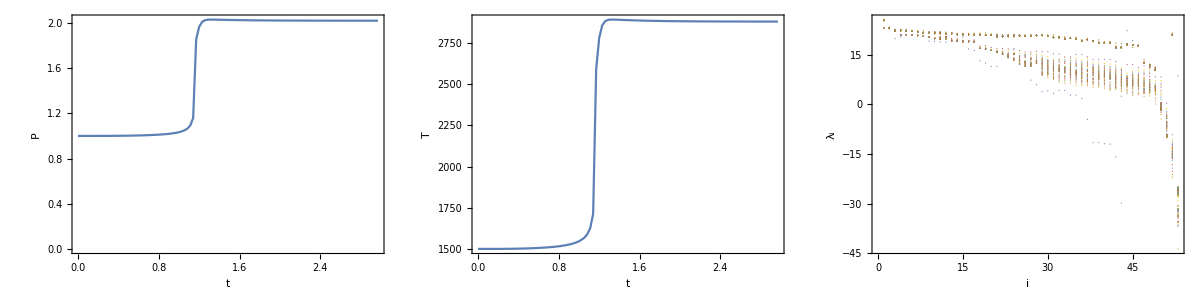

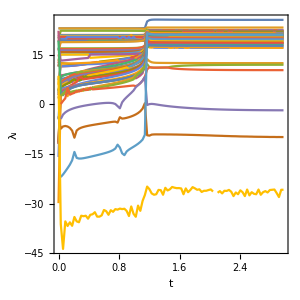

```mathematica
filebase="test"
dat=Import[filebase<>"out.dat"];
{Npoints,ns,nr}=dat[[1,1;;3]]
A=Partition[Partition[BinaryReadList[filebase<>"matrices.npy","Real64"][[17;;-1]],ns],ns];
evals=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2],ns];
evecs=Partition[Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],ns],ns];
frates=Partition[BinaryReadList[filebase<>"frates.npy","Real64"][[17;;-1]],nr];
rrates=Partition[BinaryReadList[filebase<>"rrates.npy","Real64"][[17;;-1]],nr];
Grid[{{ListPlot[Transpose[{dat[[3]]/10^-3,dat[[5]]}],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{t, P}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,5},{75,5}},AspectRatio->1],ListPlot[Transpose[{dat[[3]]/10^-3,dat[[4]]}],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{t, T}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,5},{75,5}},AspectRatio->1],ListPlot[Transpose[{dat[[3]]/10^-3,#}]&/@Transpose[Log[Abs[evals]]],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{t, Subscript[λ,i]}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,5},{75,5}},AspectRatio->1]}}]
Manipulate[MatrixPlot[A[[m]]],{m,1,Length[A],1}]
```